## Nucleation Analysis (Multi - stranded)

/homes/ht/Desktop/workspace/collagen_code/collagen_anhar1/results

| 
L: | 5.
m: | 20
N: | 5
kappa: | 1.
sigma: | 1.
Delta: | 0.12
 | 
Extension Minimum: | 0
Extension Maximum: | 20

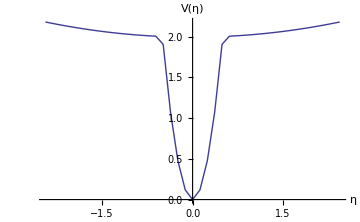

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[]}]]

PotentialData = Import["POTENTIAL_DATA","Table"];
PartitionFunction=Import["PartitionFunction_0_0.out","Table"];
FreeEnergy=Import["FreeEnergy_0_0.out","Table"];
dPartitionFunction=Import["dPartitionFunction_0_0.out","Table"];
dFreeEnergy=Import["dFreeEnergy_0_0.out","Table"];
Parameters=Import["Parameters","Grid"]
Needs["PlotLegends`"]
PlotPotentialData=ListLinePlot[{PotentialData},ImageSize->Medium,AxesOrigin->{0,0},AxesLabel->{Style["η",FontSize->18],Style["V(η)",FontSize->18]},PlotStyle->Thick,PlotRange->All]
```

Numerical Results - Partition Function

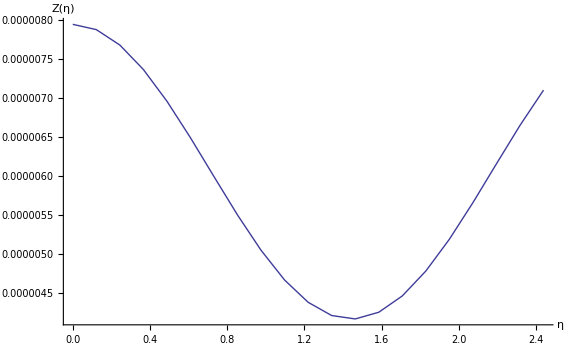

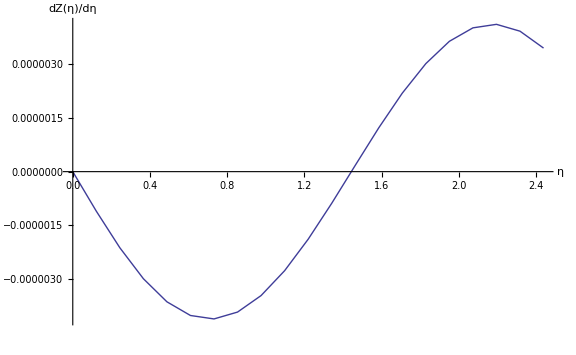

```mathematica
PartitionFunction;
PlotGraph1=ListLinePlot[{PartitionFunction},ImageSize->Large,AxesOrigin->{0,0},AxesLabel->{Style["η",FontSize->18],Style["Z(η)",FontSize->18]},PlotStyle->Thick,PlotRange->All]

dPartitionFunction;
PlotGraph1=ListLinePlot[{dPartitionFunction},ImageSize->Large,AxesOrigin->{0,0},AxesLabel->{Style["η",FontSize->18],Style["dZ(η)/dη",FontSize->18]},PlotStyle->Thick,PlotRange->All]
```

Numerical Results - Free Energy

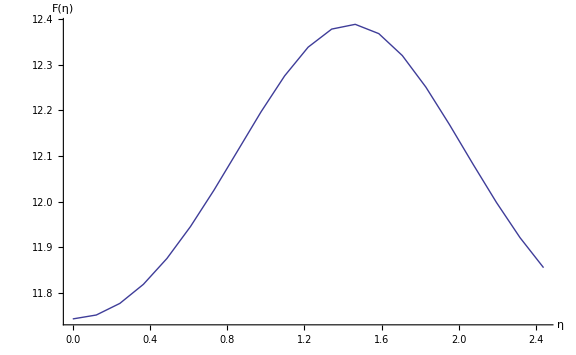

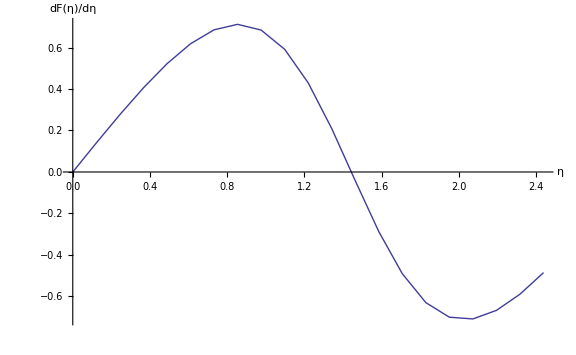

```mathematica
FreeEnergy;
PlotGraph1=ListLinePlot[{FreeEnergy},ImageSize->Large,AxesOrigin->{0,0},PlotStyle->Thick,AxesLabel->{Style["η",FontSize->18],Style["F(η)",FontSize->18]},PlotRange->All]

dFreeEnergy;
PlotGraph1=ListLinePlot[{dFreeEnergy},ImageSize->Large,AxesOrigin->{0,0},PlotStyle->Thick,AxesLabel->{Style["η",FontSize->18],Style["dF(η)/dη",FontSize->18]},PlotRange->All]
```